```mathematica
PacletDirectoryAdd[NotebookDirectory[]];
<<Project`
```

```mathematica
trained10RoundNet =Import[FileNameJoin[{NotebookDirectory[],"TrainedModels", "10_rounds.wlnet"}]];
trained30RoundNet =Import[FileNameJoin[{NotebookDirectory[],"TrainedModels", "30_rounds.wlnet"}]];

predict10RoundNet = NetExtract[trained10RoundNet,"predict"];
predict30RoundNet = NetExtract[trained30RoundNet,"predict"];
```

```mathematica
generate10RoundNet=NetJoin[NetTake[predict10RoundNet,3,"Input"->Automatic],{SequenceLastLayer[],NetExtract[predict10RoundNet,{4,"Net"}],SoftmaxLayer[]},"Input"->"Varying","Output"->NetDecoder[{"Class",Range[310]}]];

generate30RoundNet=NetJoin[NetTake[predict10RoundNet,3,"Input"->Automatic],{SequenceLastLayer[],NetExtract[predict10RoundNet,{4,"Net"}],SoftmaxLayer[]},"Input"->"Varying","Output"->NetDecoder[{"Class",Range[310]}]];
```

```mathematica
temp10RoundNet = NetTake[generate10RoundNet, 5];
sampler10RoundNet = NetTake[generate10RoundNet, -1];

temp30RoundNet = NetTake[generate10RoundNet, 5];
sampler30RoundNet = NetTake[generate10RoundNet, -1];
```

```mathematica
generateDemo[net_,start_,len_]:=Block[{obj=NetStateObject[net]},Join@NestList[{obj[#,"RandomSample"]}&,{start},len]]
generateDemoWithTemp[net_, sampler_, start_,len_,temp_: 1]:=With[{obj=NetStateObject[net]},Join@NestList[{sampler[obj[#]/temp,"RandomSample"]}&,{start},len]]
```

Generate with 10 rounds trained model

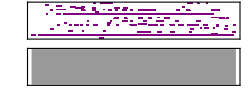

```mathematica
generated10RoundsNet = Flatten[generateDemo[generate10RoundNet,  177, 500]];
ToSound[generated10RoundsNet, True]// Quiet
```

Generate with 30 rounds trained model

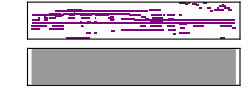

```mathematica
generated30RoundsNet = Flatten[generateDemo[generate30RoundNet,  177, 500]];
ToSound[generated30RoundsNet, True]// Quiet
```

```mathematica
Export["h.mid", %251]
```

Generate with 10 rounds trained model with temperature

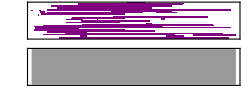

```mathematica
generated10RoundsNetTemp = Flatten[generateDemoWithTemp[temp10RoundNet, sampler10RoundNet, 177, 500, 1.8]];
ToSound[generated10RoundsNetTemp, True]// Quiet
```

Generate with 30 rounds trained model

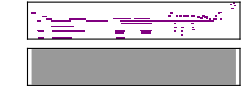

```mathematica
generated30RoundsNetTemp = Flatten[generateDemoWithTemp[temp30RoundNet, sampler10RoundNet,  177, 500, 0.9]];
ToSound[generated30RoundsNetTemp, True]// Quiet
```